## Grid count convergence

Using 1e5 macroparticles

```mathematica
(*raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-11-10-58-00.json"];*)
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-14-19-53-39.json"];
raw= Association[#]&/@raw;
```

Import::nffil: File /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-14-19-53-39.json not found during Import.

```mathematica
raw[[1]]//Keys
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Keys::invrl: The argument $Failed⟦1⟧ is not a valid Association or a list of rules.

Keys[$Failed⟦1⟧]

```mathematica
raw[[1]]
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

$Failed⟦1⟧

```mathematica
driveData = {#"gridCount",10^6#"PDrive_emitSI90_x"}&/@raw;
witnessData={#"gridCount",10^6#"PWitness_emitSI90_x"}&/@raw;
projectedData={#"gridCount",10^6#"P_emitSI90_x"}&/@raw;

allData = {driveData,witnessData,projectedData};
```

```mathematica
expr = a + b x + c x^2;
{driveNLM,witnessNLM,projectedNLM} =NonlinearModelFit[
#,
expr,
{a,b,c},
x
]&/@allData;
```

```mathematica
ListLogLinearPlot[
allData[[1;;2]],
PlotLegends->Placed[{"Drive","Witness","Projected"},{0.9,0.1}],
Frame->True,
FrameLabel->{"gridCount","Normalized emittance @ L0AFEND [μm-rad]"},
ImageSize->800,
LabelStyle->20,
PlotRange->{Automatic,Automatic}
]
```

-Graphics-

## Solenoid scan

```mathematica
(*raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-11-10-58-00.json"];*)
raw=Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/impactResults_2024-10-22-11-31-19.json"];
raw= Association[#]&/@raw;
```

```mathematica
raw[[1]]//Keys
```

{solSet,gridCount,P_emitSI90_x,P_emitSI90_y}

```mathematica
raw[[1]]
```

<|solSet→-0.37,gridCount→32.,P_emitSI90_x→4.8432×10^-6,P_emitSI90_y→4.899×10^-6|>

```mathematica
projectedData={-#"solSet",10^6#"P_emitSI90_x"}&/@raw;

allData = {projectedData};
```

```mathematica
expr = a + b x + c x^2;
{fitMin,fitMax} = {0.37,0.42};
{projectedNLM} =NonlinearModelFit[
(*#,*)
Select[#,fitMin<=#[[1]]<=fitMax&],
expr,
{a,b,c},
x
]&/@allData;
```

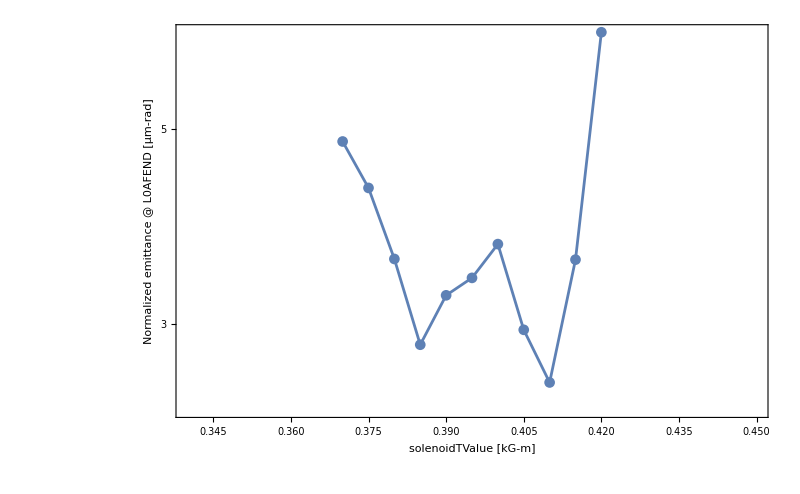

```mathematica
Show[
ListLogPlot[allData,
Frame->True,
FrameLabel->{Row[{
(*Style["solenoidTValue ",FontFamily->"Courier"], *)
Style["solenoidTValue ",FontFamily->"Fixedsys Excelsior"], 
"[kG-m]"
}],"Normalized emittance @ L0AFEND [μm-rad]"},
ImageSize->800,
LabelStyle->20,
PlotRange->{{0.34,0.45},Automatic},
Joined->True,
PlotMarkers->Automatic
]
(*,
LogPlot[{driveNLM["BestFit"],witnessNLM["BestFit"],projectedNLM["BestFit"]} ,{x,fitMin,fitMax}]*)

]
```